exercício aula 13;

```mathematica
multiplicationTable = Table[i*j, {i, 1, 12}, {j, 1, 12}]
Grid[multiplicationTable]
```

{{1,2,3,4,5,6,7,8,9,10,11,12},{2,4,6,8,10,12,14,16,18,20,22,24},{3,6,9,12,15,18,21,24,27,30,33,36},{4,8,12,16,20,24,28,32,36,40,44,48},{5,10,15,20,25,30,35,40,45,50,55,60},{6,12,18,24,30,36,42,48,54,60,66,72},{7,14,21,28,35,42,49,56,63,70,77,84},{8,16,24,32,40,48,56,64,72,80,88,96},{9,18,27,36,45,54,63,72,81,90,99,108},{10,20,30,40,50,60,70,80,90,100,110,120},{11,22,33,44,55,66,77,88,99,110,121,132},{12,24,36,48,60,72,84,96,108,120,132,144}}

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24
3 | 6 | 9 | 12 | 15 | 18 | 21 | 24 | 27 | 30 | 33 | 36
4 | 8 | 12 | 16 | 20 | 24 | 28 | 32 | 36 | 40 | 44 | 48
5 | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60
6 | 12 | 18 | 24 | 30 | 36 | 42 | 48 | 54 | 60 | 66 | 72
7 | 14 | 21 | 28 | 35 | 42 | 49 | 56 | 63 | 70 | 77 | 84
8 | 16 | 24 | 32 | 40 | 48 | 56 | 64 | 72 | 80 | 88 | 96
9 | 18 | 27 | 36 | 45 | 54 | 63 | 72 | 81 | 90 | 99 | 108
10 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 90 | 100 | 110 | 120
11 | 22 | 33 | 44 | 55 | 66 | 77 | 88 | 99 | 110 | 121 | 132
12 | 24 | 36 | 48 | 60 | 72 | 84 | 96 | 108 | 120 | 132 | 144

```mathematica
ToRomanNumeral[n_Integer] := StringReplace[IntegerString[n, "Roman"], {"IIII" -> "IV", "VIIII" -> "IX", "XXXX" -> "XL", "LXXXX" -> "XC", "CCCC" -> "CD", "DCCCC" -> "CM"}]
romanMultiplicationTable = Table[ToRomanNumeral[i*j], {i, 1, 5}, {j, 1, 5}]
Grid[romanMultiplicationTable]
```

{{I,II,III,IV,V},{II,IV,VI,VIII,X},{III,VI,IX,XII,XV},{IV,VIII,XII,XVI,XX},{V,X,XV,XX,XXV}}

I | II | III | IV | V
II | IV | VI | VIII | X
III | VI | IX | XII | XV
IV | VIII | XII | XVI | XX
V | X | XV | XX | XXV

{{RGBColor[0.5767854742250378, 0.6261227123886071, 0.3513259070009116],RGBColor[0.8502607338157013, 0.2892310688415527, 0.32450073365808474],RGBColor[0.04048526680430409, 0.6743448745630367, 0.7611071300480416],RGBColor[0.356142155803582, 0.6328508846273049, 0.5427404911132776],RGBColor[0.699340582784165, 0.7088841467743476, 0.8835120569617911],RGBColor[0.5184083682304546, 0.1441684846318474, 0.6849383204826456],RGBColor[0.010229957961565228, 0.4403767142034172, 0.0444034183676556],RGBColor[0.7150176864432973, 0.9332625207498397, 0.42462418741636654],RGBColor[0.24821630371161763, 0.20495311787114034, 0.31925133602273137],RGBColor[0.649105338509633, 0.27055323118448493, 0.12513679960462354]},{RGBColor[0.43361015088992994, 0.941101896963779, 0.06783720798701931],RGBColor[0.967951529189611, 0.27219438619050873, 0.02843204460193971],RGBColor[0.3927790753036453, 0.2709942070886311, 0.7184507051464852],RGBColor[0.6439941510439373, 0.1765238293786544, 0.4082910386757088],RGBColor[0.8416739993342217, 0.37061139541302923, 0.6615949488134218],RGBColor[0.5206294580320565, 0.2595090930372783, 0.38887357029108993],RGBColor[0.7380785644351626, 0.6149744542995981, 0.45014935466797135],RGBColor[0.9142493265106613, 0.9969107336382579, 0.3085368754536235],RGBColor[0.6454047372358314, 0.4347578982912439, 0.18704928494756357],RGBColor[0.5333604850622817, 0.19247995744005175, 0.5263191999276617]},{RGBColor[0.724231593358809, 0.18215458784808836, 0.27180935237372394],RGBColor[0.7023483578366749, 0.363732323010292, 0.6951165106273083],RGBColor[0.08221149103799319, 0.3880342093593543, 0.10301572053106733],RGBColor[3.7172878554958544*^-4, 0.9705331043643408, 0.8918169778141785],RGBColor[0.42753350609078344, 0.718035117150353, 0.21394015940183442],RGBColor[0.8267369550698644, 0.11904722891780128, 0.1844744825807576],RGBColor[0.8285999263835759, 0.5517817243585796, 0.2040518884945408],RGBColor[0.3817503525796173, 0.6598878869011118, 0.7713397751540494],RGBColor[0.40198776683383763, 0.02545072773047119, 0.39034245390883915],RGBColor[0.5587772230565751, 0.0898633730124947, 0.554791228298581]},{RGBColor[0.43690543945406213, 0.678839872723995, 0.23829111393866986],RGBColor[0.06338943028567656, 0.646789100459519, 0.3182780422629854],RGBColor[0.08378916691836014, 0.6389075503246335, 0.9785217840054221],RGBColor[0.5531154856763145, 0.8002433057996821, 0.9990659174173586],RGBColor[0.7777365891766057, 0.8151409706013257, 0.8365961637096018],RGBColor[0.4242240292992312, 0.6721776144611233, 0.4264194203016767],RGBColor[0.5564997483891776, 0.07345015127939525, 0.80256290926018],RGBColor[0.7055339839874346, 0.35704272126809466, 0.22648525824163102],RGBColor[0.8854728060819335, 0.6634207373622245, 0.22638878563711629],RGBColor[0.9310307693929087, 0.4256513270382911, 0.8322512054015305]},{RGBColor[0.3368609743338653, 0.7417796240127923, 0.24463581241159993],RGBColor[0.9038920630492671, 0.7118623542227556, 0.8149198357852416],RGBColor[0.2811337783974528, 0.5766413698280024, 0.15215388486163461],RGBColor[0.9455623116288756, 0.9377091724197817, 0.6434302783825983],RGBColor[0.26010181783977293, 0.1877181564083621, 0.21434819934262372],RGBColor[0.12941469754988377, 0.7885335503583617, 0.8325250974090541],RGBColor[0.035176884044350265, 0.5497105772360158, 0.9859637502216891],RGBColor[0.15101222280331084, 0.800178835465726, 0.8927167948223895],RGBColor[0.3640836585404976, 0.8363811409585784, 0.05336160722575256],RGBColor[0.819354807311633, 0.6271155722652526, 0.08190008274783867]},{RGBColor[0.41768935708823607, 0.5234769698006565, 0.09319730089027667],RGBColor[0.6389144583364181, 0.20310421916887966, 0.1975004526380939],RGBColor[0.5758316408260942, 0.19291459139057032, 0.8407257319679666],RGBColor[0.9388884333381573, 0.37613615576580095, 0.7319599480596852],RGBColor[0.0418186570896375, 0.09335884419361573, 0.506396633152715],RGBColor[0.7358965064690786, 0.9527027882551713, 0.08803831760711],RGBColor[0.4735431161322601, 0.06341185017619377, 0.9045849870100624],RGBColor[0.47297043853157295, 0.17355162309936278, 0.849629815403302],RGBColor[0.05723955650166368, 0.7872209396301977, 0.207704086061135],RGBColor[0.2788298384723842, 0.848010327958874, 0.161039294319266]},{RGBColor[0.3440027068298941, 0.4076713496959754, 0.7073512709488328],RGBColor[0.09126997683599414, 0.1632433769877153, 0.6522677135072774],RGBColor[0.7338781335284361, 0.5047395129552588, 0.9716208403552729],RGBColor[0.4731376663837421, 0.5855271587328783, 0.8385419086380579],RGBColor[0.2708095843977296, 0.9288373917274946, 0.4112966489099572],RGBColor[0.8838062968149467, 0.463476628204299, 0.6118993790946128],RGBColor[0.8983642658626341, 0.6182968834873919, 0.5305764180151515],RGBColor[0.4882991879160756, 0.48801357859012473, 0.9565102158380274],RGBColor[0.7693869181880271, 0.6441131370762658, 0.8833864155236737],RGBColor[0.27419606850622746, 0.7878154324909497, 0.6745859704604735]},{RGBColor[0.3460910394985304, 0.9929715903627316, 0.052174674148453226],RGBColor[0.32728583768701336, 0.7228350592094814, 0.35828668636379346],RGBColor[0.4258546444141078, 0.9131241186169836, 0.21055435450195126],RGBColor[0.8553397452692117, 0.5058700786605403, 0.18876731219577625],RGBColor[0.12963532853821258, 0.5990556040035122, 0.3032639914729396],RGBColor[0.5534092142533702, 0.015304013867761368, 0.7445138987446651],RGBColor[0.2134824296952107, 0.5087856355214593, 0.17813125031389898],RGBColor[0.5753291241380973, 0.924197536491635, 0.8503695767113362],RGBColor[0.12653857090515208, 0.6012676568355926, 0.2261735664413218],RGBColor[0.85618438983066, 0.5156639820901663, 0.2986704459263323]},{RGBColor[0.0545839297018853, 0.5015710447280244, 0.5339800315291696],RGBColor[0.2844677135638365, 0.47741102553103487, 0.4039150318010334],RGBColor[0.12785708695971887, 0.6400173389140711, 0.5034869000720541],RGBColor[0.21580328649545466, 0.2163935570204456, 0.39377192924603777],RGBColor[0.6436668868273256, 0.09310845663802025, 0.9361163182510248],RGBColor[0.005553200552374626, 0.4263246329529782, 0.37536919824330606],RGBColor[0.5397927275895658, 0.12373237312613927, 0.9314454090426978],RGBColor[0.31241709180128785, 0.4030973456613618, 0.4914328832755721],RGBColor[0.10652992076440282, 0.9380314958937441, 0.9647389226234981],RGBColor[0.5693528512822725, 0.8855340291257447, 0.5166795741575245]},{RGBColor[0.8272658545058558, 0.8455027609455847, 0.4298819471731925],RGBColor[0.39498294315154636, 0.9489232360357189, 0.20559167631510822],RGBColor[0.3518208751477605, 0.703081203324641, 0.17656788383335464],RGBColor[0.586073643095798, 0.568047027639782, 0.9709203031217604],RGBColor[0.8864332725200503, 0.6425584208494279, 0.9212099192921139],RGBColor[0.5782439201522589, 0.7084243066143887, 0.1801994503895068],RGBColor[0.6058970647685438, 0.12492929606337033, 0.7670903996441052],RGBColor[0.7883330561184745, 0.5991999105846448, 0.5273366175564556],RGBColor[0.21049124855961043, 0.8601319689707634, 0.19242027271219464],RGBColor[0.04054278855626259, 0.14510130499424445, 0.7111613385803137]}}

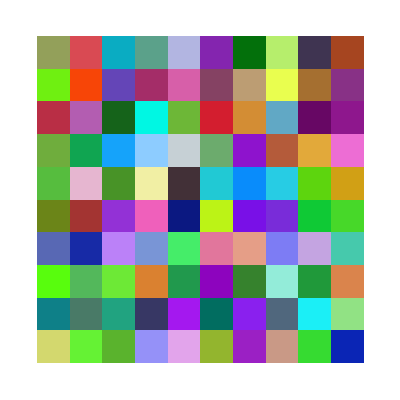

```mathematica
randomColorsGrid = Table[RandomColor[], {10}, {10}]
ArrayPlot[randomColorsGrid, ColorFunction -> (Hue[RandomReal[]] &)]
```

{{2,9,10,10,5,1,4,5,2,0},{7,9,3,0,4,4,3,0,0,1},{4,1,5,10,9,4,7,7,0,4},{2,5,2,2,8,0,4,3,8,4},{9,6,3,3,9,5,6,8,8,8},{0,9,4,3,8,5,3,0,7,5},{6,10,8,7,5,4,10,4,3,10},{7,5,0,8,1,7,4,3,0,4},{7,10,5,2,8,7,4,8,10,9},{9,9,6,10,2,8,4,6,5,0}}

{{RGBColor[0.7740274842093671, 0.1672270781442604, 0.3995519409557855],RGBColor[0.5842026931722701, 0.31265347051007386, 0.04946645474329325],RGBColor[0.6020396798700818, 0.32587354098732924, 0.28544886783108137],RGBColor[0.20605239486705562, 0.9824471808801263, 0.9038903187241223],RGBColor[0.1881205321544488, 0.7673765569097031, 0.9109434707597175],RGBColor[0.5666514217712082, 0.0047938438697419095, 0.21046137611977644],RGBColor[0.40832569011952624, 0.41671574997380767, 0.3599775353720942],RGBColor[0.8901491414426972, 0.5871675656875799, 0.7508095225079856],RGBColor[0.5426205038072927, 0.9494959605800268, 0.003950750595556052],RGBColor[0.03622066728842266, 0.8577520639336325, 0.5049136031672421]},{RGBColor[0.7174106318329205, 0.6846375342014386, 0.43664077305328575],RGBColor[0.050022815326771664, 0.025500877726482907, 0.7720440513047828],RGBColor[0.24058896198698854, 0.38020040407436584, 0.4136242831974717],RGBColor[0.35853249051977176, 0.6392589472902808, 0.8483955894773392],RGBColor[0.7806333804030381, 0.2847430905283088, 0.6191562720935695],RGBColor[0.1047509966912119, 0.38024614573902493, 0.8638079303042776],RGBColor[0.047119684886608004, 0.9515168494928554, 0.4359574693910273],RGBColor[0.26817587913209406, 0.07154924691591846, 0.7232234757385549],RGBColor[0.8913655047654807, 0.4049597481977085, 0.31826685740477756],RGBColor[0.27633347454494683, 0.15474553305809025, 0.6853399800770117]},{RGBColor[0.4832345418955295, 0.5483578060679799, 0.7689448983479918],RGBColor[0.5463232280046462, 0.2325963154257411, 0.6680081661916017],RGBColor[0.1115612217722386, 0.9322503240889288, 0.8407374104099568],RGBColor[0.6102378034132105, 0.3167754543931891, 0.9909971493420966],RGBColor[0.5240868488254489, 0.1926449612153227, 0.6554288133147339],RGBColor[0.6594477057551142, 0.6251084709455115, 0.0766074580644498],RGBColor[0.347112220496544, 0.48642541552281604, 0.7870690788463299],RGBColor[0.6696396224440935, 0.37297614421655223, 0.33068511202404816],RGBColor[0.01745883816757532, 0.6016962306466058, 0.5218393063771349],RGBColor[0.3004061823893467, 0.13437891048115835, 0.6263154790194283]},{RGBColor[0.7147755349083609, 0.46733963418698, 0.7237568061365294],RGBColor[0.2896852572667463, 0.38173171690181484, 0.23615718431550614],RGBColor[0.6327231793348564, 0.143711778347412, 0.2660812708919571],RGBColor[0.7554417379041387, 0.799074554525752, 0.35363214295002177],RGBColor[0.3266674746973399, 0.31891925712706315, 0.19599656606556004],RGBColor[0.05375147839057015, 0.08566641962506538, 0.2899034107891294],RGBColor[0.6449998061498337, 0.8924763761129093, 0.8135648777287319],RGBColor[0.04617769349933787, 0.22818615413441434, 0.6561062364549579],RGBColor[0.983790118052966, 0.8189016078179947, 0.47568275534458393],RGBColor[0.8221406238283664, 0.32274740171821703, 0.8579475981380762]},{RGBColor[0.7507351878640796, 0.5798252400583175, 0.8781354259865297],RGBColor[0.436700306507974, 0.9907468272464204, 0.11170619316746544],RGBColor[0.8616308236545707, 0.027943947040372175, 0.6113536109992335],RGBColor[0.7033388070915063, 0.7792064063153923, 0.391085289011339],RGBColor[0.5532671338475788, 0.541195316328883, 0.2384842118206938],RGBColor[0.12742521000353357, 0.7183004888330087, 0.8577161351460911],RGBColor[0.4710975546016771, 0.9490698383827065, 0.4883120717915008],RGBColor[0.3897702498581015, 0.8307364204519296, 0.7519692524080754],RGBColor[0.4000416704881078, 0.00971367815200197, 0.6086848194191945],RGBColor[0.06797312108565445, 0.7622706126547507, 0.9674463256044976]},{RGBColor[0.5673556855418393, 0.2893275604162995, 0.9410309940801069],RGBColor[0.8103555275727625, 0.8999555044689962, 0.6260122838688758],RGBColor[0.09039457939225004, 0.04720641749843835, 0.07131044260373764],RGBColor[0.46307828557225417, 0.9593071508627129, 0.8606015646369414],RGBColor[0.6170985168814356, 0.21976547014624348, 0.14581333194094115],RGBColor[0.42726016950605294, 0.5784773127415173, 0.5529630393715277],RGBColor[0.5688444818769745, 0.038831065985556856, 0.6606946110931564],RGBColor[0.7424456461594795, 0.9515360875858032, 0.5376300273466359],RGBColor[0.956385198968537, 0.7094176418969178, 0.5747691858808373],RGBColor[0.06384380208839491, 0.09259917968772524, 0.3657472819999976]},{RGBColor[0.8430396128084632, 0.9823692873822074, 0.5462948021272134],RGBColor[0.8598650772234959, 0.80633969779744, 0.37262076349247963],RGBColor[0.175976013267781, 0.33362752119044625, 0.6503253264638713],RGBColor[0.6824092709095257, 0.3870095423684057, 0.02327451828861471],RGBColor[0.09003605183310093, 0.030668173631659856, 0.024661561184941894],RGBColor[0.270123877735845, 0.33686878247047236, 0.4521370279928363],RGBColor[0.41318969788507176, 0.008184083565189182, 0.2574888307299872],RGBColor[0.3713358087248724, 0.30299273079765054, 0.8915073243559193],RGBColor[0.5231891059956586, 0.2685920869943552, 0.21135634478033105],RGBColor[0.20606447251036197, 0.8905063945954688, 0.08821496597160094]},{RGBColor[0.8930692746294717, 0.7295841743482689, 0.995620813252915],RGBColor[0.2707020746451114, 0.9931906478688071, 0.5941015913283958],RGBColor[0.0174435019372976, 0.7686613833653326, 0.6715191321697287],RGBColor[0.16934247102784528, 0.9661995609235534, 0.03390558788640585],RGBColor[0.9367982427512864, 0.4619110305835612, 0.9396563861644192],RGBColor[0.2582234996493411, 0.773691993444654, 0.25923518851917926],RGBColor[0.36931610273159654, 0.07217593885734574, 0.7230461024494279],RGBColor[0.05601319084330436, 0.8457361901536036, 0.32635641942127425],RGBColor[0.6407489220567588, 0.8025424539291401, 0.03307027023645914],RGBColor[0.3978323209406769, 0.4045251621851429, 0.16784507199313325]},{RGBColor[0.4982558641487871, 0.2941575897979689, 0.5644948997679125],RGBColor[0.14047122275581492, 0.40244747380867896, 0.33883590977776934],RGBColor[0.14135995112360034, 0.43512978998473195, 0.3336880001856264],RGBColor[0.6203346697491026, 0.2906592727979391, 0.5509967196430658],RGBColor[0.9813426066478452, 0.7881485203110594, 0.6169061459419798],RGBColor[0.7566745755323467, 0.017922491838643806, 0.07553977941450518],RGBColor[0.10094981331470532, 0.20120901617563347, 0.36091796946469534],RGBColor[0.5720210043312783, 0.15989042097649708, 0.8475855464542619],RGBColor[0.04852565701379308, 0.6382697379223148, 0.8024019924396248],RGBColor[0.8471807856382392, 0.5126255459822249, 0.019493101713934147]},{RGBColor[0.37150736552335695, 0.2894489537902014, 0.23772142374346084],RGBColor[0.7377439971520539, 0.25383103530165174, 0.5048432743543285],RGBColor[0.15175738031910568, 0.8051961114805244, 0.2894778837597878],RGBColor[0.38445097815222984, 0.16881861409607168, 0.602574876015888],RGBColor[0.69386853589812, 0.6719511586564377, 0.6572763927686063],RGBColor[0.8071501405600552, 0.7722415152356064, 0.5737624554623442],RGBColor[0.8664743234008723, 0.43982565883537905, 0.7547197916068329],RGBColor[0.4426089339895056, 0.44301526459484153, 0.6821619971889146],RGBColor[0.6199562578328324, 0.6850619005749845, 0.9486305747274784],RGBColor[0.4635718113080185, 0.46533380790227863, 0.5029188013438715]}}

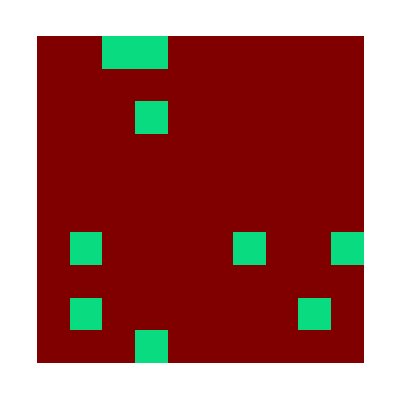

```mathematica
randomIntegersGrid = RandomInteger[{0, 10}, {10, 10}]
randomColorsGrid2 = Table[RandomColor[], {10}, {10}]
ArrayPlot[randomIntegersGrid, ColorFunction -> (randomColorsGrid2[[##]] &)]
```

```mathematica
alphabetPairs = Flatten[Table[FromCharacterCode[{i, j}], {i, 97, 122}, {j, 97, 122}]]
Grid[Partition[alphabetPairs, 26]]
```

{aa,ab,ac,ad,ae,af,ag,ah,ai,aj,ak,al,am,an,ao,ap,aq,ar,as,at,au,av,aw,ax,ay,az,ba,bb,bc,bd,be,bf,bg,bh,bi,bj,bk,bl,bm,bn,bo,bp,bq,br,bs,bt,bu,bv,bw,bx,by,bz,ca,cb,cc,cd,ce,cf,cg,ch,ci,cj,ck,cl,cm,cn,co,cp,cq,cr,cs,ct,cu,cv,cw,cx,cy,cz,da,db,dc,dd,de,df,dg,dh,di,dj,dk,dl,dm,dn,do,dp,dq,dr,ds,dt,du,dv,dw,dx,dy,dz,ea,eb,ec,ed,ee,ef,eg,eh,ei,ej,ek,el,em,en,eo,ep,eq,er,es,et,eu,ev,ew,ex,ey,ez,fa,fb,fc,fd,fe,ff,fg,fh,fi,fj,fk,fl,fm,fn,fo,fp,fq,fr,fs,ft,fu,fv,fw,fx,fy,fz,ga,gb,gc,gd,ge,gf,gg,gh,gi,gj,gk,gl,gm,gn,go,gp,gq,gr,gs,gt,gu,gv,gw,gx,gy,gz,ha,hb,hc,hd,he,hf,hg,hh,hi,hj,hk,hl,hm,hn,ho,hp,hq,hr,hs,ht,hu,hv,hw,hx,hy,hz,ia,ib,ic,id,ie,if,ig,ih,ii,ij,ik,il,im,in,io,ip,iq,ir,is,it,iu,iv,iw,ix,iy,iz,ja,jb,jc,jd,je,jf,jg,jh,ji,jj,jk,jl,jm,jn,jo,jp,jq,jr,js,jt,ju,jv,jw,jx,jy,jz,ka,kb,kc,kd,ke,kf,kg,kh,ki,kj,kk,kl,km,kn,ko,kp,kq,kr,ks,kt,ku,kv,kw,kx,ky,kz,la,lb,lc,ld,le,lf,lg,lh,li,lj,lk,ll,lm,ln,lo,lp,lq,lr,ls,lt,lu,lv,lw,lx,ly,lz,ma,mb,mc,md,me,mf,mg,mh,mi,mj,mk,ml,mm,mn,mo,mp,mq,mr,ms,mt,mu,mv,mw,mx,my,mz,na,nb,nc,nd,ne,nf,ng,nh,ni,nj,nk,nl,nm,nn,no,np,nq,nr,ns,nt,nu,nv,nw,nx,ny,nz,oa,ob,oc,od,oe,of,og,oh,oi,oj,ok,ol,om,on,oo,op,oq,or,os,ot,ou,ov,ow,ox,oy,oz,pa,pb,pc,pd,pe,pf,pg,ph,pi,pj,pk,pl,pm,pn,po,pp,pq,pr,ps,pt,pu,pv,pw,px,py,pz,qa,qb,qc,qd,qe,qf,qg,qh,qi,qj,qk,ql,qm,qn,qo,qp,qq,qr,qs,qt,qu,qv,qw,qx,qy,qz,ra,rb,rc,rd,re,rf,rg,rh,ri,rj,rk,rl,rm,rn,ro,rp,rq,rr,rs,rt,ru,rv,rw,rx,ry,rz,sa,sb,sc,sd,se,sf,sg,sh,si,sj,sk,sl,sm,sn,so,sp,sq,sr,ss,st,su,sv,sw,sx,sy,sz,ta,tb,tc,td,te,tf,tg,th,ti,tj,tk,tl,tm,tn,to,tp,tq,tr,ts,tt,tu,tv,tw,tx,ty,tz,ua,ub,uc,ud,ue,uf,ug,uh,ui,uj,uk,ul,um,un,uo,up,uq,ur,us,ut,uu,uv,uw,ux,uy,uz,va,vb,vc,vd,ve,vf,vg,vh,vi,vj,vk,vl,vm,vn,vo,vp,vq,vr,vs,vt,vu,vv,vw,vx,vy,vz,wa,wb,wc,wd,we,wf,wg,wh,wi,wj,wk,wl,wm,wn,wo,wp,wq,wr,ws,wt,wu,wv,ww,wx,wy,wz,xa,xb,xc,xd,xe,xf,xg,xh,xi,xj,xk,xl,xm,xn,xo,xp,xq,xr,xs,xt,xu,xv,xw,xx,xy,xz,ya,yb,yc,yd,ye,yf,yg,yh,yi,yj,yk,yl,ym,yn,yo,yp,yq,yr,ys,yt,yu,yv,yw,yx,yy,yz,za,zb,zc,zd,ze,zf,zg,zh,zi,zj,zk,zl,zm,zn,zo,zp,zq,zr,zs,zt,zu,zv,zw,zx,zy,zz}

aa | ab | ac | ad | ae | af | ag | ah | ai | aj | ak | al | am | an | ao | ap | aq | ar | as | at | au | av | aw | ax | ay | az
ba | bb | bc | bd | be | bf | bg | bh | bi | bj | bk | bl | bm | bn | bo | bp | bq | br | bs | bt | bu | bv | bw | bx | by | bz
ca | cb | cc | cd | ce | cf | cg | ch | ci | cj | ck | cl | cm | cn | co | cp | cq | cr | cs | ct | cu | cv | cw | cx | cy | cz
da | db | dc | dd | de | df | dg | dh | di | dj | dk | dl | dm | dn | do | dp | dq | dr | ds | dt | du | dv | dw | dx | dy | dz
ea | eb | ec | ed | ee | ef | eg | eh | ei | ej | ek | el | em | en | eo | ep | eq | er | es | et | eu | ev | ew | ex | ey | ez
fa | fb | fc | fd | fe | ff | fg | fh | fi | fj | fk | fl | fm | fn | fo | fp | fq | fr | fs | ft | fu | fv | fw | fx | fy | fz
ga | gb | gc | gd | ge | gf | gg | gh | gi | gj | gk | gl | gm | gn | go | gp | gq | gr | gs | gt | gu | gv | gw | gx | gy | gz
ha | hb | hc | hd | he | hf | hg | hh | hi | hj | hk | hl | hm | hn | ho | hp | hq | hr | hs | ht | hu | hv | hw | hx | hy | hz
ia | ib | ic | id | ie | if | ig | ih | ii | ij | ik | il | im | in | io | ip | iq | ir | is | it | iu | iv | iw | ix | iy | iz
ja | jb | jc | jd | je | jf | jg | jh | ji | jj | jk | jl | jm | jn | jo | jp | jq | jr | js | jt | ju | jv | jw | jx | jy | jz
ka | kb | kc | kd | ke | kf | kg | kh | ki | kj | kk | kl | km | kn | ko | kp | kq | kr | ks | kt | ku | kv | kw | kx | ky | kz
la | lb | lc | ld | le | lf | lg | lh | li | lj | lk | ll | lm | ln | lo | lp | lq | lr | ls | lt | lu | lv | lw | lx | ly | lz
ma | mb | mc | md | me | mf | mg | mh | mi | mj | mk | ml | mm | mn | mo | mp | mq | mr | ms | mt | mu | mv | mw | mx | my | mz
na | nb | nc | nd | ne | nf | ng | nh | ni | nj | nk | nl | nm | nn | no | np | nq | nr | ns | nt | nu | nv | nw | nx | ny | nz
oa | ob | oc | od | oe | of | og | oh | oi | oj | ok | ol | om | on | oo | op | oq | or | os | ot | ou | ov | ow | ox | oy | oz
pa | pb | pc | pd | pe | pf | pg | ph | pi | pj | pk | pl | pm | pn | po | pp | pq | pr | ps | pt | pu | pv | pw | px | py | pz
qa | qb | qc | qd | qe | qf | qg | qh | qi | qj | qk | ql | qm | qn | qo | qp | qq | qr | qs | qt | qu | qv | qw | qx | qy | qz
ra | rb | rc | rd | re | rf | rg | rh | ri | rj | rk | rl | rm | rn | ro | rp | rq | rr | rs | rt | ru | rv | rw | rx | ry | rz
sa | sb | sc | sd | se | sf | sg | sh | si | sj | sk | sl | sm | sn | so | sp | sq | sr | ss | st | su | sv | sw | sx | sy | sz
ta | tb | tc | td | te | tf | tg | th | ti | tj | tk | tl | tm | tn | to | tp | tq | tr | ts | tt | tu | tv | tw | tx | ty | tz
ua | ub | uc | ud | ue | uf | ug | uh | ui | uj | uk | ul | um | un | uo | up | uq | ur | us | ut | uu | uv | uw | ux | uy | uz
va | vb | vc | vd | ve | vf | vg | vh | vi | vj | vk | vl | vm | vn | vo | vp | vq | vr | vs | vt | vu | vv | vw | vx | vy | vz
wa | wb | wc | wd | we | wf | wg | wh | wi | wj | wk | wl | wm | wn | wo | wp | wq | wr | ws | wt | wu | wv | ww | wx | wy | wz
xa | xb | xc | xd | xe | xf | xg | xh | xi | xj | xk | xl | xm | xn | xo | xp | xq | xr | xs | xt | xu | xv | xw | xx | xy | xz
ya | yb | yc | yd | ye | yf | yg | yh | yi | yj | yk | yl | ym | yn | yo | yp | yq | yr | ys | yt | yu | yv | yw | yx | yy | yz
za | zb | zc | zd | ze | zf | zg | zh | zi | zj | zk | zl | zm | zn | zo | zp | zq | zr | zs | zt | zu | zv | zw | zx | zy | zz

{1,4,3,5,2}

-Graphics-

-Graphics-

-Graphics-

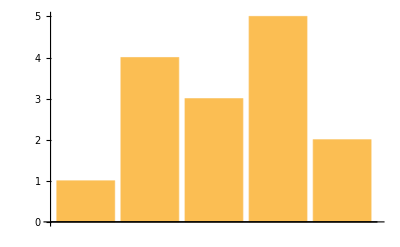

-Graphics-

```mathematica
data = {1, 4, 3, 5, 2}
pieChart = PieChart[data]
numberLine = ListLinePlot[Transpose[{Range[5], data}], PlotStyle -> PointSize[Medium], Mesh -> All, MeshStyle -> Red]
linePlot = ListPlot[data, Joined -> True]
barChart = BarChart[data]
GraphicsGrid[{{pieChart, numberLine}, {linePlot, barChart}}]
```

{{Hue[0.],Hue[0.],Hue[0.],Hue[0.],Hue[0.],Hue[0.],Hue[0.],Hue[0.],Hue[0.],Hue[0.],Hue[0.],Hue[0.],Hue[0.],Hue[0.],Hue[0.],Hue[0.],Hue[0.],Hue[0.],Hue[0.],Hue[0.],Hue[0.]},{Hue[0.],Hue[0.0025000000000000005],Hue[0.005000000000000001],Hue[0.0075000000000000015],Hue[0.010000000000000002],Hue[0.0125],Hue[0.015000000000000003],Hue[0.0175],Hue[0.020000000000000004],Hue[0.022500000000000003],Hue[0.025],Hue[0.027500000000000004],Hue[0.030000000000000006],Hue[0.0325],Hue[0.035],Hue[0.037500000000000006],Hue[0.04000000000000001],Hue[0.04250000000000001],Hue[0.045000000000000005],Hue[0.04750000000000001],Hue[0.05]},{Hue[0.],Hue[0.005000000000000001],Hue[0.010000000000000002],Hue[0.015000000000000003],Hue[0.020000000000000004],Hue[0.025],Hue[0.030000000000000006],Hue[0.035],Hue[0.04000000000000001],Hue[0.045000000000000005],Hue[0.05],Hue[0.05500000000000001],Hue[0.06000000000000001],Hue[0.065],Hue[0.07],Hue[0.07500000000000001],Hue[0.08000000000000002],Hue[0.08500000000000002],Hue[0.09000000000000001],Hue[0.09500000000000001],Hue[0.1]},{Hue[0.],Hue[0.0075000000000000015],Hue[0.015000000000000003],Hue[0.022500000000000006],Hue[0.030000000000000006],Hue[0.037500000000000006],Hue[0.04500000000000001],Hue[0.05250000000000001],Hue[0.06000000000000001],Hue[0.06750000000000002],Hue[0.07500000000000001],Hue[0.08250000000000002],Hue[0.09000000000000002],Hue[0.09750000000000002],Hue[0.10500000000000002],Hue[0.11250000000000002],Hue[0.12000000000000002],Hue[0.12750000000000003],Hue[0.13500000000000004],Hue[0.14250000000000004],Hue[0.15000000000000002]},{Hue[0.],Hue[0.010000000000000002],Hue[0.020000000000000004],Hue[0.030000000000000006],Hue[0.04000000000000001],Hue[0.05],Hue[0.06000000000000001],Hue[0.07],Hue[0.08000000000000002],Hue[0.09000000000000001],Hue[0.1],Hue[0.11000000000000001],Hue[0.12000000000000002],Hue[0.13],Hue[0.14],Hue[0.15000000000000002],Hue[0.16000000000000003],Hue[0.17000000000000004],Hue[0.18000000000000002],Hue[0.19000000000000003],Hue[0.2]},{Hue[0.],Hue[0.0125],Hue[0.025],Hue[0.037500000000000006],Hue[0.05],Hue[0.0625],Hue[0.07500000000000001],Hue[0.08750000000000001],Hue[0.1],Hue[0.1125],Hue[0.125],Hue[0.1375],Hue[0.15000000000000002],Hue[0.1625],Hue[0.17500000000000002],Hue[0.1875],Hue[0.2],Hue[0.21250000000000002],Hue[0.225],Hue[0.23750000000000002],Hue[0.25]},{Hue[0.],Hue[0.015000000000000003],Hue[0.030000000000000006],Hue[0.04500000000000001],Hue[0.06000000000000001],Hue[0.07500000000000001],Hue[0.09000000000000002],Hue[0.10500000000000002],Hue[0.12000000000000002],Hue[0.13500000000000004],Hue[0.15000000000000002],Hue[0.16500000000000004],Hue[0.18000000000000005],Hue[0.19500000000000003],Hue[0.21000000000000005],Hue[0.22500000000000003],Hue[0.24000000000000005],Hue[0.25500000000000006],Hue[0.2700000000000001],Hue[0.2850000000000001],Hue[0.30000000000000004]},{Hue[0.],Hue[0.0175],Hue[0.035],Hue[0.05250000000000001],Hue[0.07],Hue[0.08750000000000001],Hue[0.10500000000000002],Hue[0.12250000000000003],Hue[0.14],Hue[0.15750000000000003],Hue[0.17500000000000002],Hue[0.19250000000000003],Hue[0.21000000000000005],Hue[0.22750000000000004],Hue[0.24500000000000005],Hue[0.2625],Hue[0.28],Hue[0.29750000000000004],Hue[0.31500000000000006],Hue[0.3325000000000001],Hue[0.35000000000000003]},{Hue[0.],Hue[0.020000000000000004],Hue[0.04000000000000001],Hue[0.06000000000000001],Hue[0.08000000000000002],Hue[0.1],Hue[0.12000000000000002],Hue[0.14],Hue[0.16000000000000003],Hue[0.18000000000000002],Hue[0.2],Hue[0.22000000000000003],Hue[0.24000000000000005],Hue[0.26],Hue[0.28],Hue[0.30000000000000004],Hue[0.32000000000000006],Hue[0.3400000000000001],Hue[0.36000000000000004],Hue[0.38000000000000006],Hue[0.4]},{Hue[0.],Hue[0.022500000000000003],Hue[0.045000000000000005],Hue[0.06750000000000002],Hue[0.09000000000000001],Hue[0.1125],Hue[0.13500000000000004],Hue[0.15750000000000003],Hue[0.18000000000000002],Hue[0.2025],Hue[0.225],Hue[0.24750000000000003],Hue[0.2700000000000001],Hue[0.29250000000000004],Hue[0.31500000000000006],Hue[0.3375],Hue[0.36000000000000004],Hue[0.38250000000000006],Hue[0.405],Hue[0.42750000000000005],Hue[0.45]},{Hue[0.],Hue[0.025],Hue[0.05],Hue[0.07500000000000001],Hue[0.1],Hue[0.125],Hue[0.15000000000000002],Hue[0.17500000000000002],Hue[0.2],Hue[0.225],Hue[0.25],Hue[0.275],Hue[0.30000000000000004],Hue[0.325],Hue[0.35000000000000003],Hue[0.375],Hue[0.4],Hue[0.42500000000000004],Hue[0.45],Hue[0.47500000000000003],Hue[0.5]},{Hue[0.],Hue[0.027500000000000004],Hue[0.05500000000000001],Hue[0.08250000000000002],Hue[0.11000000000000001],Hue[0.1375],Hue[0.16500000000000004],Hue[0.19250000000000003],Hue[0.22000000000000003],Hue[0.24750000000000003],Hue[0.275],Hue[0.30250000000000005],Hue[0.33000000000000007],Hue[0.35750000000000004],Hue[0.38500000000000006],Hue[0.41250000000000003],Hue[0.44000000000000006],Hue[0.4675000000000001],Hue[0.49500000000000005],Hue[0.5225000000000001],Hue[0.55]},{Hue[0.],Hue[0.030000000000000006],Hue[0.06000000000000001],Hue[0.09000000000000002],Hue[0.12000000000000002],Hue[0.15000000000000002],Hue[0.18000000000000005],Hue[0.21000000000000005],Hue[0.24000000000000005],Hue[0.2700000000000001],Hue[0.30000000000000004],Hue[0.33000000000000007],Hue[0.3600000000000001],Hue[0.39000000000000007],Hue[0.4200000000000001],Hue[0.45000000000000007],Hue[0.4800000000000001],Hue[0.5100000000000001],Hue[0.5400000000000001],Hue[0.5700000000000002],Hue[0.6000000000000001]},{Hue[0.],Hue[0.0325],Hue[0.065],Hue[0.09750000000000002],Hue[0.13],Hue[0.1625],Hue[0.19500000000000003],Hue[0.22750000000000004],Hue[0.26],Hue[0.29250000000000004],Hue[0.325],Hue[0.35750000000000004],Hue[0.39000000000000007],Hue[0.42250000000000004],Hue[0.45500000000000007],Hue[0.48750000000000004],Hue[0.52],Hue[0.5525000000000001],Hue[0.5850000000000001],Hue[0.6175],Hue[0.65]},{Hue[0.],Hue[0.035],Hue[0.07],Hue[0.10500000000000002],Hue[0.14],Hue[0.17500000000000002],Hue[0.21000000000000005],Hue[0.24500000000000005],Hue[0.28],Hue[0.31500000000000006],Hue[0.35000000000000003],Hue[0.38500000000000006],Hue[0.4200000000000001],Hue[0.45500000000000007],Hue[0.4900000000000001],Hue[0.525],Hue[0.56],Hue[0.5950000000000001],Hue[0.6300000000000001],Hue[0.6650000000000001],Hue[0.7000000000000001]},{Hue[0.],Hue[0.037500000000000006],Hue[0.07500000000000001],Hue[0.11250000000000002],Hue[0.15000000000000002],Hue[0.1875],Hue[0.22500000000000003],Hue[0.2625],Hue[0.30000000000000004],Hue[0.3375],Hue[0.375],Hue[0.41250000000000003],Hue[0.45000000000000007],Hue[0.48750000000000004],Hue[0.525],Hue[0.5625],Hue[0.6000000000000001],Hue[0.6375000000000001],Hue[0.675],Hue[0.7125],Hue[0.75]},{Hue[0.],Hue[0.04000000000000001],Hue[0.08000000000000002],Hue[0.12000000000000002],Hue[0.16000000000000003],Hue[0.2],Hue[0.24000000000000005],Hue[0.28],Hue[0.32000000000000006],Hue[0.36000000000000004],Hue[0.4],Hue[0.44000000000000006],Hue[0.4800000000000001],Hue[0.52],Hue[0.56],Hue[0.6000000000000001],Hue[0.6400000000000001],Hue[0.6800000000000002],Hue[0.7200000000000001],Hue[0.7600000000000001],Hue[0.8]},{Hue[0.],Hue[0.04250000000000001],Hue[0.08500000000000002],Hue[0.12750000000000003],Hue[0.17000000000000004],Hue[0.21250000000000002],Hue[0.25500000000000006],Hue[0.29750000000000004],Hue[0.3400000000000001],Hue[0.38250000000000006],Hue[0.42500000000000004],Hue[0.4675000000000001],Hue[0.5100000000000001],Hue[0.5525000000000001],Hue[0.5950000000000001],Hue[0.6375000000000001],Hue[0.6800000000000002],Hue[0.7225000000000001],Hue[0.7650000000000001],Hue[0.8075000000000001],Hue[0.8500000000000001]},{Hue[0.],Hue[0.045000000000000005],Hue[0.09000000000000001],Hue[0.13500000000000004],Hue[0.18000000000000002],Hue[0.225],Hue[0.2700000000000001],Hue[0.31500000000000006],Hue[0.36000000000000004],Hue[0.405],Hue[0.45],Hue[0.49500000000000005],Hue[0.5400000000000001],Hue[0.5850000000000001],Hue[0.6300000000000001],Hue[0.675],Hue[0.7200000000000001],Hue[0.7650000000000001],Hue[0.81],Hue[0.8550000000000001],Hue[0.9]},{Hue[0.],Hue[0.04750000000000001],Hue[0.09500000000000001],Hue[0.14250000000000004],Hue[0.19000000000000003],Hue[0.23750000000000002],Hue[0.2850000000000001],Hue[0.3325000000000001],Hue[0.38000000000000006],Hue[0.42750000000000005],Hue[0.47500000000000003],Hue[0.5225000000000001],Hue[0.5700000000000002],Hue[0.6175],Hue[0.6650000000000001],Hue[0.7125],Hue[0.7600000000000001],Hue[0.8075000000000001],Hue[0.8550000000000001],Hue[0.9025000000000001],Hue[0.9500000000000001]},{Hue[0.],Hue[0.05],Hue[0.1],Hue[0.15000000000000002],Hue[0.2],Hue[0.25],Hue[0.30000000000000004],Hue[0.35000000000000003],Hue[0.4],Hue[0.45],Hue[0.5],Hue[0.55],Hue[0.6000000000000001],Hue[0.65],Hue[0.7000000000000001],Hue[0.75],Hue[0.8],Hue[0.8500000000000001],Hue[0.9],Hue[0.9500000000000001],Hue[1.]}}

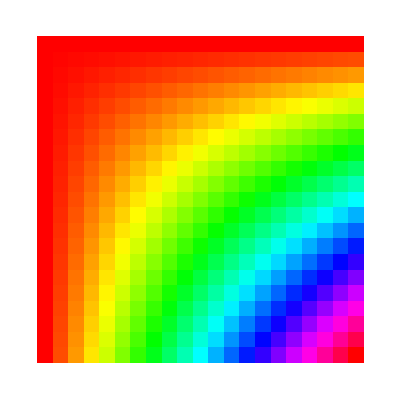

```mathematica
hueValuesXY = Table[Hue[x*y], {x, 0, 1, 0.05}, {y, 0, 1, 0.05}]
ArrayPlot[hueValuesXY]
```

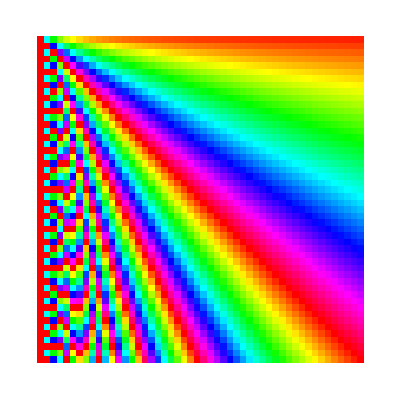

```mathematica
hueValuesXY2 = Table[Hue[x/y], {x, 1, 50}, {y, 1, 50}]
ArrayPlot[hueValuesXY2]
```

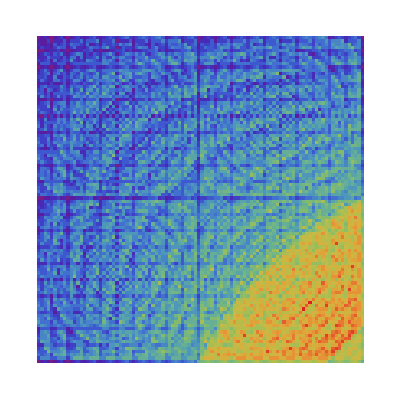

```mathematica
romanStringLengths = Table[StringLength[ToRomanNumeral[i*j]], {i, 1, 100}, {j, 1, 100}]
ArrayPlot[romanStringLengths, ColorFunction -> "Rainbow"]
```

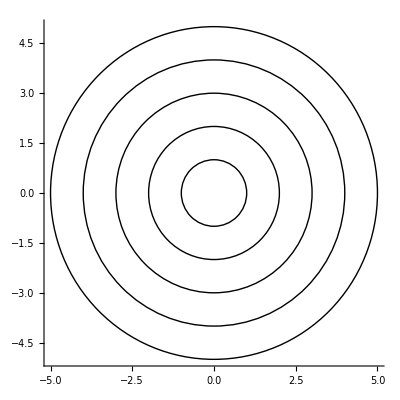

```mathematica
"aula 14";

Graphics[Table[Circle[{0, 0}, r], {r, 1, 5}], Axes -> True]
```

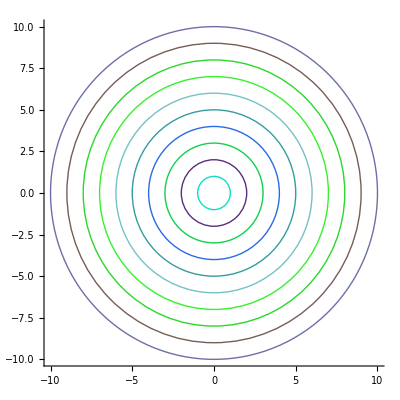

```mathematica
Graphics[Table[{RandomColor[], Circle[{0, 0}, r]}, {r, 1, 10}], Axes -> True]
```

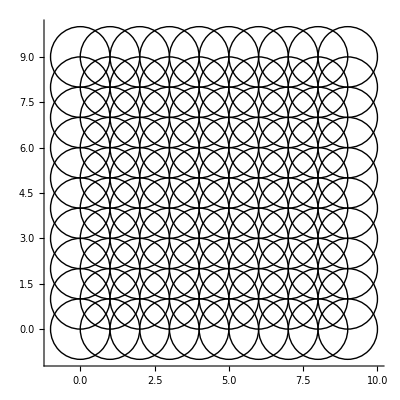

```mathematica
Graphics[Table[Circle[{x, y}, 1], {x, 0, 9}, {y, 0, 9}], Axes -> True]
```

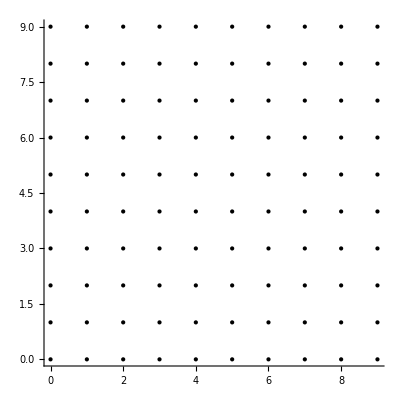

-Graphics-

```mathematica
Graphics[Table[Point[{x, y}], {x, 0, 9}, {y, 0, 9}], Axes -> True]
```

```mathematica
Manipulate[
 Graphics[Table[Circle[{0, 0}, r], {r, 1, n}], Axes → True],
 {{n, 1, "Number of Circles"}, 1, 20, 1}
]
```

```mathematica
Manipulate[
 Graphics[Table[Circle[{0, 0}, r], {r, 1, n}], Axes -> True],
 {{n, 1, "Number of Circles"}, 1, 20, 1}
]
```

```mathematica
Graphics3D[
 Table[
  {RandomColor[], Sphere[RandomInteger[{0, 10}, 3]]}, 
  {50}
 ]
]
```

-Graphics3D-

```mathematica
Graphics3D[
 Table[
  {RGBColor[x/10, y/10, z/10], Sphere[{x, y, z}, 0.5]}, 
  {x, 0, 10}, {y, 0, 10}, {z, 0, 10}
 ], 
 Boxed → False
]
```

-Graphics3D-

```mathematica
Manipulate[
 Graphics[Table[Circle[{t*x, 0}, x], {x, 1, 10}], Axes -> True],
 {{t, 0, "t"}, -2, 2, 0.1}
]
```

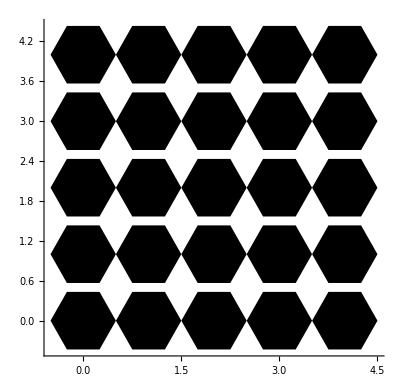

```mathematica
hexagon = Polygon[Table[{Cos[2 Pi k/6], Sin[2 Pi k/6]}, {k, 0, 5}]/2];
Graphics[Table[Translate[hexagon, {x, y}], {x, 0, 4}, {y, 0, 4}], Axes -> True]
```

```mathematica
randomPoints = RandomInteger[{0, 50}, {50, 3}];
Graphics3D[{Line[randomPoints]}, Axes -> True]
```

-Graphics3D-